## Supplement: Evaluation of Expressions

## Learning Objectives

### Principles of Evaluation

Evaluation of expressions

Tracing an evaluation process

The six-step evaluation process

Setting and removing attributes

Examples of special attributes in play

Overriding Hold attributes

Hold attributes of built-in functions

## Principles of Evaluation

Wolfram Language is at its core a pattern-matching term-rewriting system. How is it that terms are actually rewritten in the process of evaluation?

### Evaluation

Whenever you enter an expression, Wolfram Language evaluates the expression and then returns the result.

All operations in Wolfram Language can also be viewed in a uniform way as examples of evaluation:

Computation 5+6⟶11
Simplification x-3x+1⟶1-2x
Execution x=5⟶5

```mathematica
5+6
```

```mathematica
x-3x+1
```

```mathematica
x=2
```

```mathematica
a=2;
b=3;
c=(a+b)^2
```

Wolfram Language is an infinite evaluation system. This means that whenever you enter an expression, Wolfram Language will repeatedly apply definitions to transform the expression until no more definitions apply.

### Tracing an Evaluation

When you are trying to understand what the Wolfram System is doing, it can be worthwhile to check intermediate steps in the evaluation process.

Trace can be used to generate a list of all expressions used in a particular evaluation process:

```mathematica
Trace[5+6]
```

{5+6,11}

```mathematica
Trace[5^3+6^2+1 ]
```

{{5^3,125},{6^2,36},125+36+1,162}

By setting the option TraceOriginal to True, you can get Trace also to look at expressions before function arguments have been evaluated:

```mathematica
Trace[5^3+6^2+1 ,TraceOriginal->True]
```

{5^3+6^2+1,{Plus},{5^3,{Power},{5},{3},5^3,125},{6^2,{Power},{6},{2},6^2,36},{1},125+36+1,162}

## Evaluation of Head

When you press Shift+Enter, Wolfram Language evaluates the expression in the following order:

Head[elem1, elem2, elem3, ...]

Evaluate the head of the expression.

Evaluate elements.

Standard Evaluation Procedure: Evaluate all the elements in turn.

Nonstandard Evaluation Procedure: Evaluate selected elements in turn, or do not evaluate any element.

Apply transformations associated with the attributes Orderless, Listable and Flat.

Apply any definitions that you have given.

Apply any built-in definitions.

Evaluate the result.

### Example

Consider computing the sine of 10.0:

```mathematica
Sin[10.0]
```

-0.544021

```mathematica
Trace[Sin[10.0],TraceOriginal->True]
```

{Sin[10.],{Sin},{10.},Sin[10.],-0.544021}

Now, consider the following list and evaluation:

```mathematica
funs={Sin,Cos,Tan};
funs[[1]][10.0]
```

-0.544021

This produces the same result, because funs[[1]] gets evaluated to Sin first:

```mathematica
Trace[funs[[1]][10.0] ,TraceOriginal->True]
```

{funs⟦1⟧[10.],{funs⟦1⟧,{Part},{funs,{Sin,Cos,Tan}},{1},{Sin,Cos,Tan}⟦1⟧,Sin},{10.},Sin[10.],-0.544021}

## Evaluation of Elements

### Standard Evaluation

Head[elem1, elem2, elem3, ...]

Evaluate the head of the expression.

Evaluate elements.

Standard Evaluation Procedure: Evaluate all the elements in turn.

Nonstandard Evaluation Procedure: Evaluate selected elements in turn, or do not evaluate any element.

Apply transformations associated with the attributes Orderless, Listable and Flat.

Apply any definitions that you have given.

Apply any built-in definitions.

Evaluate the result.

Each element in the expression is evaluated in turn:

```mathematica
Clear[x,y,z];
x=1;
y=2;
z=3;
```

```mathematica
Trace[Plus[x,y,z],TraceOriginal->True]
```

{x+y+z,{Plus},{x,1},{y,2},{z,3},1+2+3,6}

## Nonstandard Evaluation Procedure

Head[elem1, elem2, elem3, ...]

Evaluate the head of the expression.

Evaluate elements.

Standard Evaluation Procedure: Evaluate all the elements in turn.

Nonstandard Evaluation Procedure: Evaluate selected elements in turn, or do not evaluate any element.

Apply transformations associated with the attributes Orderless, Listable and Flat.

Apply any definitions that you have given.

Apply any built-in definitions.

Evaluate the result.

Some functions have special attributes that prevent their arguments from being evaluated as they would be under the standard evaluation procedure.

### Nonstandard Evaluation

HoldFirst specifies that the first argument to a function is to be maintained in an unevaluated form:

```mathematica
Clear[x,y,z];
x=1;
y=2;
z=3;
```

```mathematica
ClearAll[f]
f[x^2,y^2,z^2]
```

f[1,4,9]

```mathematica
ClearAll[f]
SetAttributes[f,HoldFirst]
f[x^2,y^2,z^2]
```

f[x^2,4,9]

HoldRest specifies that all but the first argument to a function are to be maintained in an unevaluated form:

```mathematica
ClearAll[f]
SetAttributes[f,HoldRest]
f[x^2,y^2,z^2]
```

f[4,y^2,z^2]

HoldAll specifies that all arguments to a function are to be maintained in an unevaluated form:

```mathematica
ClearAll[f]
SetAttributes[f,HoldAll]
f[x^2,y^2,z^2]
```

f[x^2,y^2,z^2]

### Example

Plot holds its arguments to prevent the result from being useless or nonsensical:

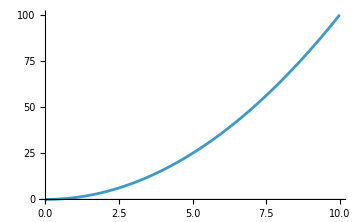

```mathematica
Clear[x];
x=2;
Plot[x^2,{x,0,10}]
```

If x were to be evaluated right away, the plot would be useless:

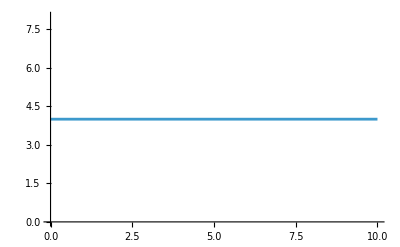

```mathematica
Plot[2^2,{x,0,10}]
```

Similarly for the following expression, x^2 should not be evaluated right away:

```mathematica
x=2;
Table[x^2,{x,0,5}]
```

{0,1,4,9,16,25}

The tutorial on Evaluation provides more information on the standard evaluation sequence and nonstandard argument evaluation.

## Attributes: Orderless, Listable and Flat

Head[elem1, elem2, elem3, ...]

Evaluate the head of the expression.

Evaluate elements.

Standard Evaluation Procedure: Evaluate all the elements in turn.

Nonstandard Evaluation Procedure: Evaluate selected elements in turn, or do not evaluate any element.

Apply transformations associated with the attributes Orderless, Listable and Flat.

Apply any definitions that you have given.

Apply any built-in definitions.

Evaluate the result.

HoldFirst, HoldRest and HoldAll are responsible for instantiating the nonstandard evaluation procedure in Step 2 of the evaluation loop, but they are not the only attributes that a function can have in Wolfram Language. The attributes Orderless, Listable and Flat carry with them transformation rules that comprise Step 3 of the loop.

### Orderless

Orderless indicates that elements should automatically be sorted into canonical order. It corresponds to the mathematical property of commutativity:

```mathematica
ClearAll[f]
f[x_,y_]:=x^y
```

```mathematica
f[3,2]
```

9

```mathematica
f[2,3]
```

8

```mathematica
SetAttributes[f,Orderless];
```

```mathematica
f[3,2]
```

8

```mathematica
f[2,3]
```

8

```mathematica
Trace[f[3,2],TraceOriginal->True]
```

{f[3,2],{f},{3},{2},f[3,2],f[2,3],2^3,{Power},{2},{3},2^3,8}

If function arguments are restricted (e.g. by head), functions with the Orderless attribute will try to match the restrictions by reordering their arguments:

```mathematica
SetAttributes[magnifyImage,Orderless];
magnifyImage[img_Image,fact_Integer]:=Magnify[img,fact]
```

```mathematica
magnifyImage[2,-Graphics-]
magnifyImage[-Graphics-,2]
```

### Listable

A function with the Listable attribute automatically threads over lists that appear as its arguments:

```mathematica
ClearAll[f];
SetAttributes[f,Listable]
```

```mathematica
f[{a,b,c,d}]
```

{f[a],f[b],f[c],f[d]}

Many built-in functions have the Listable attribute:

```mathematica
Sin[{a,b,c}]
```

{Sin[a],Sin[b],Sin[c]}

```mathematica
Attributes[Sin]
```

{Listable,NumericFunction,Protected}

Over a two-dimensional list:

```mathematica
f[{{a,b,c},{p,q,r}}]
```

{{f[a],f[b],f[c]},{f[p],f[q],f[r]}}

With two arguments:

```mathematica
f[{a,b,c},{p,q,r}]
```

{f[a,p],f[b,q],f[c,r]}

### Flat

A function with the Flat attribute flattens out its arguments when nested instances of that same function exist as its arguments. This attribute corresponds to the mathematical property of associativity:

```mathematica
ClearAll[f]
SetAttributes[f,Flat]
```

```mathematica
f[1,f[2,3],f[f[4,5],6],7]
```

f[1,2,3,4,5,6,7]

```mathematica
Plus[1,Plus[2,3,Plus[4,5]]] ===Plus[1,2,3,4,5] (*1+((2+3+(4+5)))===1+2+3+4+5*)
```

True

```mathematica
Times[1,Times[2,3,Times[4,5]]]===Times[1,2,3,4,5] (*1*((2*3*(4*5)))===1*2*3*4*5*)
```

True

```mathematica
Attributes/@{Plus,Times}
```

{{Flat,Listable,NumericFunction,OneIdentity,Orderless,Protected},{Flat,Listable,NumericFunction,OneIdentity,Orderless,Protected}}

Flatten can perform the same operation for functions that do not have this attribute:

```mathematica
Flatten[g[1,g[2,3],g[g[4,5],6],7]]
```

g[1,2,3,4,5,6,7]

```mathematica
Flatten[{1,{2,3},{{4,5},6},7}]
```

{1,2,3,4,5,6,7}

## Applying Definitions

Head[elem1, elem2, elem3, ...]

Evaluate the head of the expression.

Evaluate elements.

Standard Evaluation Procedure: Evaluate all the elements in turn.

Nonstandard Evaluation Procedure: Evaluate selected elements in turn, or do not evaluate any element.

Apply transformations associated with the attributes Orderless, Listable and Flat.

Apply any definitions that you have given.

Apply any built-in definitions.

Evaluate the result.

### Modifying Built-in Definitions

Definitions are nothing but transformation rules for any expression. You can define such rules not only for functions that you add to Wolfram Language but also for intrinsic functions that are already built into Wolfram Language. As a result, you can enhance or otherwise modify the features of built-in Wolfram Language functions.

This capability is powerful, but potentially dangerous.

To avoid the possibility of changing built-in functions by mistake, Wolfram Language "protects" all built-in functions from redefinition:

```mathematica
Attributes[Print]
```

{Protected}

If you try to set a definition for Print, it will show an error:

```mathematica
Print["Wolfie"]:="\[WolframLanguageLogo]"<>"Wolfie"<>"\[WolframLanguageLogo]"
```

SetDelayed::write: Tag Print in Print[Wolfie] is Protected.

$Failed

You can apply Unprotect to the function and add the new definition:

```mathematica
Unprotect[Print];
```

Set the new definition:

```mathematica
Print["Wolfie"]:="\[WolframLanguageLogo]"<>"Wolfie"<>"\[WolframLanguageLogo]"
```

```mathematica
?Print
```

```mathematica
Print["Wolfie"]
```

\[WolframLanguageLogo]Wolfie\[WolframLanguageLogo]

```mathematica
Trace[Print["Wolfie"],TraceOriginal->True]
```

{Print[Wolfie],{Print},{Wolfie},Print[Wolfie],\[WolframLanguageLogo]<>Wolfie<>\[WolframLanguageLogo],{StringJoin},{\[WolframLanguageLogo]},{Wolfie},{\[WolframLanguageLogo]},\[WolframLanguageLogo]<>Wolfie<>\[WolframLanguageLogo],\[WolframLanguageLogo]Wolfie\[WolframLanguageLogo]}

```mathematica
Print["Wolfram"]
```

Wolfram

```mathematica
Trace[Print["Wolfram"],TraceOriginal->True]
```

Wolfram

{Print[Wolfram],{Print},{Wolfram},Print[Wolfram],{MakeBoxes[Wolfram,StandardForm],{MakeBoxes},MakeBoxes[Wolfram,StandardForm],"Wolfram"},Null}

Apply Unset to the new definition:

```mathematica
Print["Wolfie"]=.
```

Apply Protect to it to prevent future mistakes:

```mathematica
Protect[Print];
```

Definitions you give can override built-in features of Wolfram Language.

NB: In general, Wolfram Language tries to use your definitions before it uses built-in definitions.

## Evaluating the Result

Head[elem1, elem2, elem3, ...]

Evaluate the head of the expression.

Evaluate elements.

Standard Evaluation Procedure: Evaluate all the elements in turn.

Nonstandard Evaluation Procedure: Evaluate selected elements in turn, or do not evaluate any element.

Apply transformations associated with the attributes Orderless, Listable and Flat.

Apply any definitions that you have given.

Apply any built-in definitions.

Evaluate the result.

After applying the definitions, any remaining evaluations on the result will be done:

```mathematica
ClearAll[f]
Attributes[f]={HoldAll};
f[x_]:=Sin[x]
```

```mathematica
?f
```

```mathematica
k=10.0;
f[k]
```

-0.544021

```mathematica
Trace[f[k],TraceOriginal->True]
```

{f[k],{f},f[k],Sin[k],{Sin},{k,10.},Sin[10.],-0.544021}

Note that k gets evaluated after the definition of f is applied. Compare to the evaluation without the HoldAll attribute:

```mathematica
k=10.0;
g[x_]:=Sin[x]
Trace[g[k],TraceOriginal->True]
```

{g[k],{g},{k,10.},g[10.],Sin[10.],{Sin},{10.},Sin[10.],-0.544021}

## All the Steps

Head[elem1, elem2, elem3, ...]

Evaluate the head of the expression.

Evaluate elements.

Standard Evaluation Procedure: Evaluate all the elements in turn.

Nonstandard Evaluation Procedure: Evaluate selected elements in turn, or do not evaluate any element.

Apply transformations associated with the attributes Orderless, Listable and Flat.

Apply any definitions that you have given.

Apply any built-in definitions.

Evaluate the result.

```mathematica
x=15;
y=10;
z=5;
```

```mathematica
fn=Plus;
```

```mathematica
fn[x,y,z]
```

30

```mathematica
Trace[fn[x,y,z],TraceOriginal->True]
```

{fn[x,y,z],{fn,Plus},{x,15},{y,10},{z,5},15+10+5,30}

(Step 1) fn is evaluated to Plus

{{fn,Plus},{x,15},{y,10},{z,5},15+10+5,30}

(Step 2) x, y and z are evaluated

{{fn,Plus},{x,15},{y,10},{z,5},15+10+5,30}

(Step 3) The attribute Orderless is applied

{15,10,5} becomes {5,10,15} (although this cannot be seen in the trace).

(Step 5 & 6) The definition of Plus is applied and the result is evaluated; Step 4 is not relevant in this case.

{{fn,Plus},{x,15},{y,10},{z,5},15+10+5,30}

## Overriding Hold* Attributes

Sometimes you need to force evaluation of arguments in functions with Hold* attributes:

```mathematica
ClearAll[f,x];
SetAttributes[f,HoldAll]
```

```mathematica
x=10;
f[x]
```

f[x]

Method 1: You can force the evaluation using Evaluate:

```mathematica
f[Evaluate[x]]
```

f[10]

Method 2: You can assign a constant value using With:

```mathematica
With[{y=10},f[y]]
```

f[10]

Method 3: You can use ReplaceAll to replace the value of the symbol in the output:

```mathematica
Clear[y]
f[y]/.y->10
```

f[10]

Method 4: You can use ReplaceAll with an injector pattern:

```mathematica
10/.num_:>f[num]
```

f[10]

### Example 1: Build a Pure Function from an Existing Expression

The following approach for defining a pure function does not work:

```mathematica
Clear[x,expr]
```

```mathematica
expr=x^2+2 x+1
```

1+2 x+x^2

```mathematica
Function[{x},expr][5]
```

1+2 x+x^2

Function does not evaluate its arguments:

```mathematica
Attributes[Function]
```

{HoldAll,Protected}

You can force evaluation of the argument:

```mathematica
Function[{x},Evaluate[expr]][5]
```

36

### Example 2: Build a List of Pure Functions

The iterator in a Table cannot inject values inside a function if it has the HoldAll attribute:

```mathematica
ClearAll[i,f]
```

```mathematica
ClearAll[f];
SetAttributes[f,HoldAll];
```

```mathematica
Table[f[i],{i,1,5}]
```

{f[i],f[i],f[i],f[i],f[i]}

The pure function has the HoldAll attribute:

```mathematica
Attributes[Function]
```

{HoldAll,Protected}

Here is a list of constants:

```mathematica
a={10,20,30,40,50};
```

Trying to use the constant values from the list does not work with Table:

```mathematica
fnList=Table[a[[i]]*Sin[#]&,{i,5}]
```

{a⟦i⟧ Sin[#1]&,a⟦i⟧ Sin[#1]&,a⟦i⟧ Sin[#1]&,a⟦i⟧ Sin[#1]&,a⟦i⟧ Sin[#1]&}

```mathematica
fnList[[1]]
```

a⟦i⟧ Sin[#1]&

```mathematica
fnList[[1]][10.]
```

Part::pkspec1: The expression i cannot be used as a part specification.

-0.544021 {10,20,30,40,50}⟦i⟧

Instead you can try ReplaceAll with a pattern:

```mathematica
fnList2=Range[5]/.(x_Integer:>(a[[x]]*Sin[#]&))
```

{a⟦1⟧ Sin[#1]&,a⟦2⟧ Sin[#1]&,a⟦3⟧ Sin[#1]&,a⟦4⟧ Sin[#1]&,a⟦5⟧ Sin[#1]&}

```mathematica
fnList2[[1]][10.0]
```

-5.44021

### Example 3: Inject Pre-constructed Options

The following attempt to insert options does not work for functions with the HoldAll attribute:

```mathematica
plotOptions={PlotPoints->10,MaxRecursion->2,PlotStyle->Red};
Plot[x^2,{x,0,10},plotOptions]
```

Plot::nonopt: Options expected (instead of plotOptions) beyond position 2 in Plot[x^2,{x,0,10},plotOptions]. An option must be a rule or a list of rules.

Plot[x^2,{x,0,10},plotOptions]

```mathematica
nintegrateOptions={ Exclusions->(Sin[x^2+y]==0),WorkingPrecision->10};
NIntegrate[1/(√Sin[x^2+y]),{x,-5,5},{y,-5,5}, nintegrateOptions]
```

NIntegrate::ilim: Invalid integration variable or limit(s) in {Exclusions→Sin[x^2+y]==0,WorkingPrecision→10}.

NIntegrate[1/(√Sin[x^2+y]),{x,-5,5},{y,-5,5},nintegrateOptions]

```mathematica
Attributes[{Plot,NIntegrate}]
```

{{HoldAll,Protected,ReadProtected},{HoldAll,Protected}}

Instead, the options expression needs to be evaluated first:

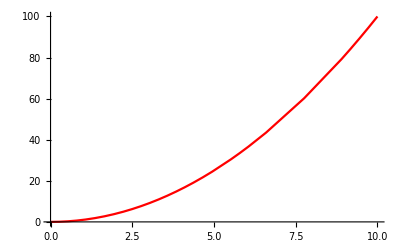

```mathematica
Plot[x^2,{x,0,10},Evaluate[plotOptions]]
```

```mathematica
NIntegrate[1/(√Sin[x^2+y]),{x,-5,5},{y,-5,5}, Evaluate[nintegrateOptions]]
```

81.84747968-84.70573498 ⅈ

### Example 4: Symbolic Evaluations inside *Plot Functions

Various plot functions evaluate the function after substituting iterator values. So you may run into the following issues:

```mathematica
Plot[D[Sin[x],x],{x,0,10}]
```

General::ivar: 0.000204286 is not a valid variable.

General::ivar: 0.204286 is not a valid variable.

General::ivar: 0.408368 is not a valid variable.

General::stop: Further output of General::ivar will be suppressed during this calculation.

-Graphics-

```mathematica
RegionPlot[Integrate[y/(2 Sqrt[x y]),x]<1,{x,-2,2},{y,-2,2}]
```

Integrate::ilim: Invalid integration variable or limit(s) in -1.99979.

-Graphics-

Evaluate can come to the rescue:

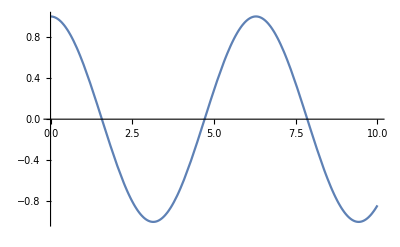

```mathematica
Plot[Evaluate[D[Sin[x],x]],{x,0,10}]
```

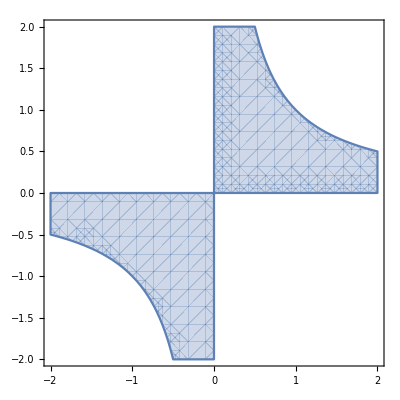

```mathematica
RegionPlot[Evaluate[Integrate[y/(2 Sqrt[x y]),x]<1],{x,-2,2},{y,-2,2}]
```

### Example 5: Styling for a List of Expressions inside *Plot Functions

Plot functions apply styling uniformly unless an explicit list structure is provided.

The List structure is not visible to Plot and RegionPlot:

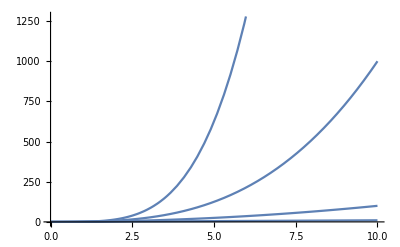

```mathematica
Plot[Table[x^i,{i,1,4}],{x,0,10},PlotLegends->"Expressions"]
```

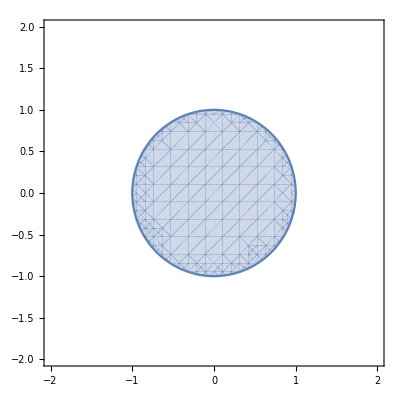

```mathematica
RegionPlot[Table[x^2+y^2<n,{n,1,3}],{x,-2,2},{y,-2,2},PlotLegends->"Expressions"]
```

Evaluate causes the list structure to manifest:

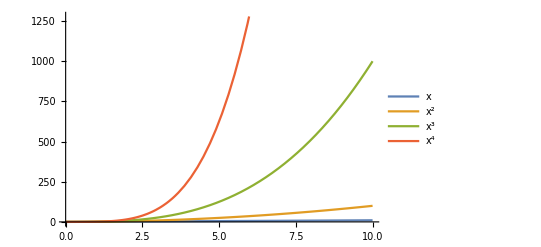

```mathematica
Plot[Evaluate[Table[x^i,{i,1,4}]],{x,0,10},PlotLegends->"Expressions"]
```

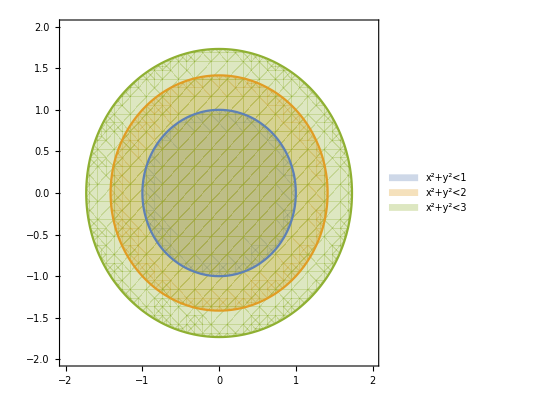

```mathematica
RegionPlot[Evaluate[Table[x^2+y^2<n,{n,1,3}]],{x,-2,2},{y,-2,2},PlotLegends->"Expressions"]
```

## References

Evaluation

Evaluation of Expressions

Attributes

The Standard Evaluation Procedure

Non-Standard Evaluation